```mathematica
Tau=2Pi;
Exact[a_]:=-Zeta[3]/(4 Tau a^3)//N;
Middle[xs_]:=xs[[Floor[(Length[xs]+1)/2]]];
WithXRegion[a_,b_][xs_]:=Block[{n=Length[xs]},Table[{a + (b-a) i/n, xs[[i]]},{i,1,n}]];
SimpsonSum[xs_]:=Block[{n=Length[xs]},
xs[[1]] + 4Sum[xs[[j]], {j, 2, n-1, 2}] + 2Sum[xs[[j]],{j,3,n-1,2}]+xs[[n]]
];
SimpsonIntegrate[f_,{a_,b_,npts_}]:=Block[{
dx=(b-a)/npts,
pts=Table[f[x],{x,a,b,dx}]
},
dx/3 SimpsonSum[pts]
];

M[a_, L_, w_, resolution_:0] := Module[{n,x,da,coefficient, E},
n =If[resolution≠ 0,resolution, Max[30, 5 L / a // Ceiling]];
If[w == 0, Return[0.5 IdentityMatrix[2n]]];

x[i_]:=L (i-1/2)/n;
da[dx_]:=Sqrt[a^2 + dx^2];

coefficient[α_,β_][i_,j_]:=If[α==β,
If[i==j,0,0],
-a w L/(n Tau) BesselK[1, w da[x[i]-x[j]]] / da[x[i] - x[j]]
]//N;
E =Table[Table[coefficient[α,β][i,j],{i,1,n},{j,1,n}],{α,0,1},{β,0,1}]//ArrayFlatten;
E + IdentityMatrix[2n]
];

v[a_,L_,w_,resolution_:0]:=Module[{n,s,x,da,K0,K1,q,V,source},
n =If[resolution≠0,resolution,Max[30, 5 L / a // Ceiling]];
If[w == 0, Return[Table[0, {i, 1, n}, {j, 1, n}]]];

s[i_]:=(i-1/2)/n;
x[i_]:=L(i-1/2)/n;
da[dx_]:=Sqrt[a^2 + dx^2];
K0=BesselK[0,#]&; K1=BesselK[1,#]&;

q[i_,j_,k_]:=Piecewise[{
(*{???, k==j},*)
{ 2 w a L/Tau^2 NIntegrate[K0[w L Abs[s[j]-t]]  K1[w da[x[i]-L t]] / da[x[i]-L t],{t,(k-1)/n,k/n}],Abs[j-k]/n≤1}
},2w a L/Tau^2 * 1/n         K0[w L Abs[s[j]-s[k]]] K1[w da[x[i] - x[k]] / da[x[i] - x[k]]]
]//N//Re;
(***)
source[α_,β_][i_,j_]:= If[α==β,0,
-1/Tau K0[w da[x[i]-x[j]]]-NIntegrate[-w a/Tau K1[w da[x[i]-ξ]]/da[x[i]-ξ] * -1/Tau K0[w Abs[x[j]-ξ]],{ξ,0,L}](*Sum[q[i,j,k],{k,1,n}]*)
]//Re;
V=ParallelTable[source[0,1][i,j],{i,1,n},{j,{Floor[n/2]}}];
ArrayFlatten[{{ConstantArray[0,{Length[V],Length[V[[1]]]}], V},{V,ConstantArray[0,{Length[V],Length[V[[1]]]}]}}]
];

x[a_,L_,w_,resolution_:0]:=Module[{coefficients, source,p},
coefficients = M[a,L,w,resolution];
source = v[a,L,w,resolution];
p=LinearSolve[coefficients, source];
Table[p[[k,1]],{k,1,Length[p]/2}]
];

P[a_,L_,w_,resolution_:0]:=If[w==0,0,x[a,L,w,resolution]//Middle];

Force[a_,L_,precision_:10,resolution_:0]:=Module[{integrand,dw,pts,result,wmax},
integrand[w_]:=w^2 P[a,L,w,resolution];

wmax = 4.5 /a;

dw =wmax/precision;
pts=Monitor[Table[integrand[w],{w,0,wmax,dw}],ProgressIndicator[w,{0,wmax}]];

result=dw/3 SimpsonSum[pts];
If[Abs[Last[pts]/result]≥ 0.1, Print["Integral might have been cut off before convergence"]];
If[Abs[Last[pts]/result]≤0.001,Print["Integral might have been cut off long after convergence"]];
result
];

Exact[1]
```

-0.0478283

```mathematica
M[1,10,1,50]//ListPlot3D
```

-Graphics3D-

```mathematica
P[1,10,1,30]
```

-0.0139375

```mathematica
Force[1,10]
```

Part::partd: Part specification $Aborted⟦1⟧ is longer than depth of object.

Last::normal: Nonatomic expression expected at position 1 in Last[$Aborted].

0.15 (Symbol+$Aborted⟦1⟧)

```mathematica
P[1,10,1,50]
```

-0.000364808

```mathematica
Force[1,20]
```

Part::partd: Part specification $Aborted⟦1⟧ is longer than depth of object.

1/5 (Symbol+$Aborted⟦1⟧)

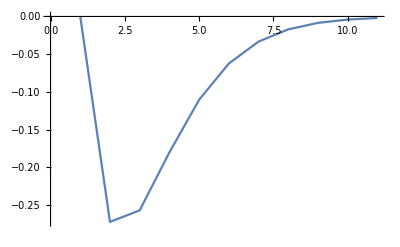

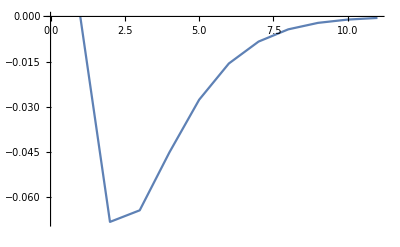

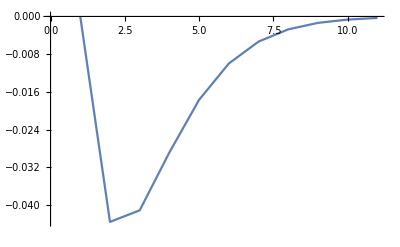

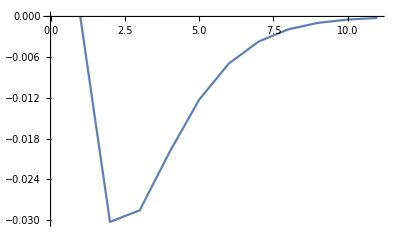

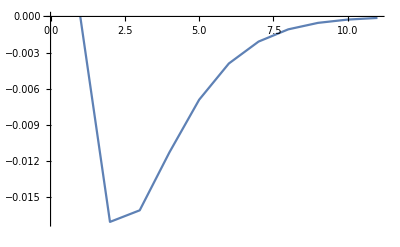

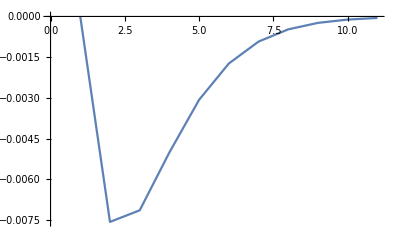

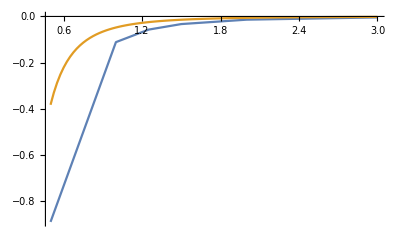

```mathematica
Module[{apts,Fpts,exactPts},
apts={0.1,0.5,1, 1.25,1.5,2,3};
Fpts=Monitor[
Table[{a,Force[a,10a]},{a,apts}],
{a,ProgressIndicator[a,{First[apts],Last[apts]}]}
];
exactPts=Table[{a,2Exact[a]},{a,First[apts],Last[apts],(Last[apts]-First[apts])/100}];
ListLinePlot[{Fpts,exactPts},PlotRange->All]
]
```

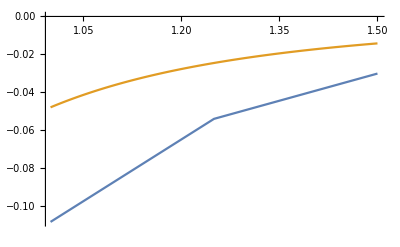

```mathematica
plot=%
```

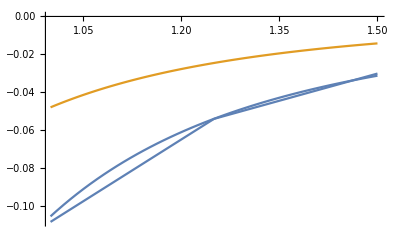

```mathematica
Show[plot,Plot[2.2Exact[a],{a,1,1.5}]]
```